# 动手工作纸：+/- 2 trailing sigma

## 每一步都有可照抄的示例。请在紧跟着的空输入格里亲手键入，再按 Shift+Enter。

## 0. 你会用到的三个符号

data：数据库读回的两腿日线；spread：固定 beta 后的价差列表；window：滚动窗口的交易日数量。先不要试图一次理解全部，按顺序做。

## 1. 载入工具

先照抄并运行下面这行。Get 的意思是读取另一个 Wolfram Language 文件；分号不是必须，但通常用来不显示无关输出。

Get[FileNameJoin[{NotebookDirectory[], "AACENXDailyMovingAverageLab.wl"}]]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"AACENXDailyMovingAverageLab.wl"}]]
```

如果没有红色报错，继续。这个步骤不会读取数据库。

## 2. 定义 pair，读取共同日线

照抄下面三行。{ } 是列表；@@ 表示把 pair 中的两个元素分别传给 AACENXDailyRead；Keys[data] 用来查看 data 中保存了哪些东西。

pair = {"AA", "CENX"};
data = AACENXDailyRead @@ pair;
Keys[data]

```mathematica
pair={"AA","CENX"};
data=AACENXDailyRead@@pair;
Keys[data]
```

{Dates,Y,X,PricesY,PricesX}

预期：输出类似 {"Dates", "Y", "X", "PricesY", "PricesX"}。若只显示符号 data，说明前一步或数据库读取没有成功。

## 3. 归一化两条腿，建立 fixed-beta spread

照抄。双中括号 [[1]] 取列表第一个元素；First[...] 是同一件事的函数写法。y 和 x 都从 1 开始，beta 是你固定指定的对冲比率。

dates = data["Dates"];
y = data["PricesY"]/First[data["PricesY"]];
x = data["PricesX"]/First[data["PricesX"]];
beta = .642;
spread = y - beta x;
Length /@ {dates, y, x, spread}

```mathematica
dates=data["Dates"];
y=data["PricesY"]/First[data["PricesY"]];
```

```mathematica
x=data["PricesX"]/First[data["PricesX"]];
beta=0.642;
spread=y-beta x;
Length/@{dates,y,x,spread}
```

{1092,1092,1092,1092}

预期：最后一行输出四个相同的整数。现在先试 beta = 0 和 beta = 1，重新运行最后两行，观察 spread 如何改变。

## 4. 建立 trailing mean，并把日期贴对

照抄。window = 20 表示连续 20 个交易日。mean 的第一个结果是 spread 的第 1 至第 20 个点的平均，所以它必须贴到第 20 个日期；Wolfram 列表从 1 开始。

window = 20;
mean = MovingAverage[spread, window];
meanDates = dates[[window ;;]];
{Length[spread], Length[mean], Length[meanDates]}

```mathematica
window=20;
mean=MovingAverage[spread,window];
meanDates=dates[[window;;]];
{Length[spread],Length[mean],Length[meanDates]}
```

{1092,1073,1073}

预期：后两个长度相同，且都比 spread 少 19。注意 `;;` 的意思是“从 window 一直到最后”。

## 5. 建立 trailing sigma

照抄。Partition[spread, window, 1] 会产生一串窗口：第一个是第 1 到 20 点，第二个是第 2 到 21 点。/@ 的意思是“对列表里的每一个窗口都做 StandardDeviation”。

windows = Partition[spread, window, 1];
sigma = StandardDeviation /@ windows;
{Length[windows], Length[sigma], Length[mean], Length[meanDates]}

```mathematica
windows=Partition[spread,window,1];
sigma=StandardDeviation/@windows;
{Length[windows],Length[sigma],Length[mean],Length[meanDates]}
```

{1073,1073,1073,1073}

预期：四个长度全相同。若 sigma 只有一个数，说明你误写成了 StandardDeviation[spread]；那是整段样本 sigma，不是 trailing sigma。

## 6. 写出 +2 sigma 与 -2 sigma

照抄。Wolfram 会把等长列表逐项相加或相减。

upper = mean + 2 sigma;
lower = mean - 2 sigma;
{Length[upper], Length[lower], Length[meanDates]}

```mathematica
upper=mean+2*sigma;
lower=mean-2 sigma;
{Length[upper],Length[lower],Length[meanDates]}
```

{1073,1073,1073}

预期：三个相同的长度。

## 7. 最后才画图

照抄这段。蓝线是完整 spread；白线和红线使用 meanDates，因此从第 20 日才开始。不要先追求漂亮，先让图成功出现。

DateListPlot[
 {Transpose[{dates, spread}], Transpose[{meanDates, mean}],
  Transpose[{meanDates, upper}], Transpose[{meanDates, lower}]},
 Joined -> True,
 PlotStyle -> {Blue, White, Red, Red},
 Background -> RGBColor[.055, .07, .10],
 Frame -> True, FrameStyle -> White, LabelStyle -> White,
 GridLines -> {None, Automatic}, GridLinesStyle -> Gray,
 PlotRange -> All, ImageSize -> 1050]

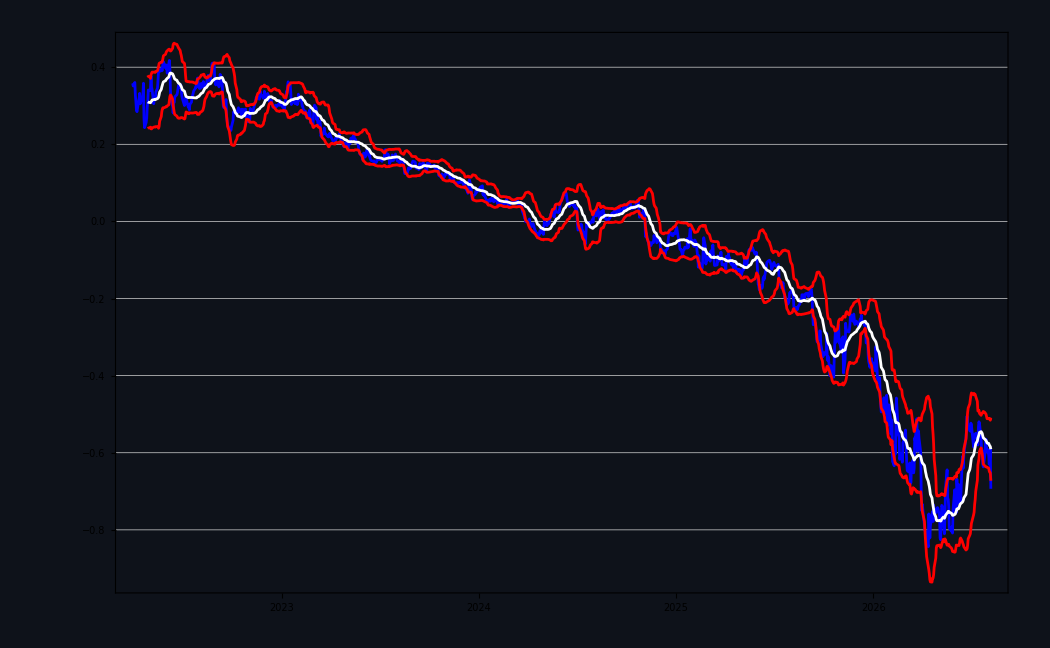

```mathematica
DateListPlot[
{Transpose[{dates, spread}],Transpose[{meanDates,mean}],
Transpose[{meanDates,upper}],Transpose[{meanDates,lower}]},
Joined->True,
PlotStyle->{Blue,White,Red,Red},
Background->RGBColor[.055,.07,.10],
Frame->True, FrameStyle->White,LabelStyle->White,
GridLines->{None,Automatic},GridLinesStyle->Gray,
PlotRange->All,ImageSize->1050

]
```

现在你已经亲手构造了：spread、trailing mean、trailing sigma、upper/lower bands 和正确日期对齐。完成后再打开 trailing_sigma_lesson.ipynb；它会解释为什么这套写法没有未来函数，以及 ±2 sigma 不能直接理解为 95% 胜率。

## 8. 附加实验：正弦 spread 的 trailing sigma

这一节不读数据库。请从上到下运行；随后只改 beta、cenxAmplitudeSlope 或 window，再从这一节的第一格重新运行。这里故意让 CENX 的振幅随时间线性变大，于是你能看见固定 beta 面对振幅变化时，spread 与 trailing sigma 如何变化。

```mathematica
days = Range[0, 240];
beta = .3;
aaAmplitude = .30;
cenxAmplitude = .50;
cenxAmplitudeSlope = 0.8;

aa = 1 + aaAmplitude Sin[2 Pi days/20];
cenx = 1 + cenxAmplitude (1 + cenxAmplitudeSlope days/Max[days]) Sin[2 Pi days/20];
spread = aa - beta cenx;

{Take[spread, 5], Take[spread, -5]}
```

{{0.7,0.746198,0.78758,0.820139,0.840756},{0.669566,0.674516,0.681779,0.690575,0.7}}

先观察这一格：beta = .6 正好等于初始振幅比 .30/.50；但 CENX 的振幅继续长大，原本的抵消会逐渐失效。把 cenxAmplitudeSlope 改成 0 再运行，会看到 spread 退成一条水平线。

```mathematica
window = 40;
mean = MovingAverage[spread, window];
meanDays = days[[window ;;]];

windows = Partition[spread, window, 1];
sigma = StandardDeviation /@ windows;
upper = mean + 2 sigma;
lower = mean - 2 sigma;

{Dimensions[windows], Length[spread], Length[mean], Length[sigma], First[sigma], Last[sigma]}
```

{{202,40},241,202,202,0.100325,0.028886}

这一格正是你刚才卡住的地方：StandardDeviation 的输入必须是一段数据，例如一个 20 点窗口；不能写 StandardDeviation[20]。这里 /@ 的意思是：对 windows 里的每一段 20 点数据，各做一次 StandardDeviation。Range[0,240] 一共 241 点，因此会得到 222 个 20 点窗口。

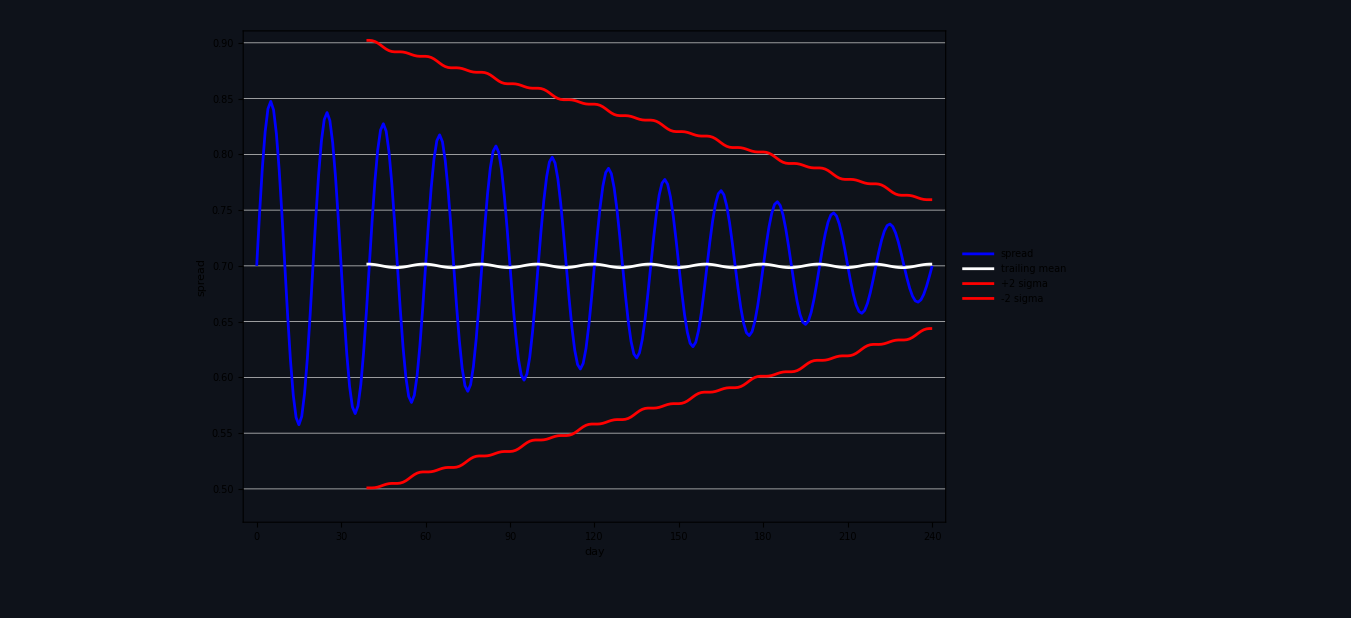

```mathematica
ListLinePlot[
 {Transpose[{days, spread}], Transpose[{meanDays, mean}],
  Transpose[{meanDays, upper}], Transpose[{meanDays, lower}]},
 Joined -> True,
 PlotStyle -> {Blue, White, Red, Red},
 Background -> RGBColor[.055, .07, .10],
 Frame -> True, FrameStyle -> White, LabelStyle -> White,
 FrameLabel -> {"day", "spread"},
 GridLines -> {None, Automatic}, GridLinesStyle -> Gray,
 PlotLegends -> {"spread", "trailing mean", "+2 sigma", "-2 sigma"},
 PlotRange -> All, ImageSize -> 1000]
```

建议按这个顺序试：① cenxAmplitudeSlope = 0、beta = .6；② slope = .8、beta = .6；③ slope = .8、beta = .3；④ window 改成 10 和 40。每次都从本节第一格重新运行。你会发现：带宽不是价格本身的振幅，而是最近 window 天内 spread 围绕其自身 trailing mean 的离散程度。